## 3. domača naloga

#### 1. naloga

Definiramo konstante in usterzne vektorje:

```mathematica
v0 = {10, 3}
GG = 9.81
H = 10
```

{10,3}

9.81

10

```mathematica
a = {0, -GG}
x0 ={0, H}
```

{0,-9.81}

{0,10}

Formule iz fizike, nam povedo naslednje:
	v(t) = v_o + a t
	x(t) = x_o + v_ot + at^2/2

Z upoštevanjem teh formul lahko zapišemo naslednji izraz.

```mathematica
v[t_] :={v0[[1]], v0[[2]] - GG*t}
```

Lahko pa zgornji enačbi zapišemo tudi v vektorski obliki, saj sta veljavni za vsako komponento posebej.

```mathematica
{v0[[1]], v0[[2]] - GG*t}
v0 + a*t
```

{10,3-9.81 t}

{10,3-9.81 t}

Zapišimo sedaj obe funkciji kar preko vektorske oblike. Pozor: namesto simbola “mali x” smo uporabili simbol “veliki X”. To pa zato, ker si ponavadi simbolov x, y, ... ne želimo “zasesti”, saj imamo potem tipično težave pri reševanju enačb.

```mathematica
v[t_] := v0 + a*t
X[t_] := x0 + v0*t + a*t^2/2
```

Točko določa funkcija X[t]. S pomočjo te sestavimo ustrezen grafični objekt.

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]}
```

Oglejmo si rezultat. Pri vrednosti t = 1. Dodamo tudi koordinatne osi ter nastavimo območje izrisa.

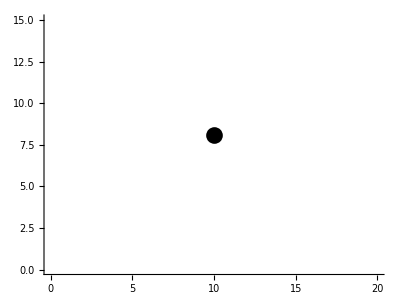

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

Uporabimo funkcijo Manipulate, da si ogledamo, kako se gibljej točka.

```mathematica
Manipulate[Graphics[SlikaTocke[t], Axes->True, PlotRange-> {{0,20}, {0, 15}}], {t, 0, 3}]
```

Narišemo še vektor hitrosti iz točke.

```mathematica
SlikaVektorja[t_] := Arrow[{X[t],X[t]+v[t]}]
```

```mathematica
Manipulate[Graphics[{{SlikaVektorja[t]},Thick}, Axes->True, AspectRatio->Automatic,PlotRange->{{0,20},{0,15}}], {t, 0, 3}]
```

Narišemo sliko žoge in vektorja po eni sekundi.

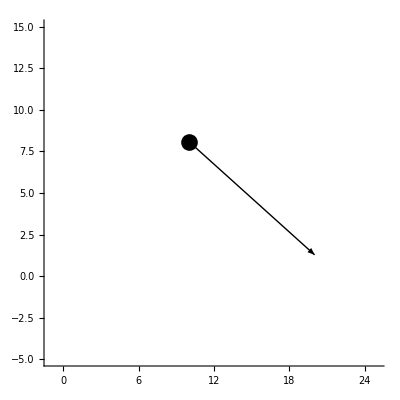

```mathematica
Graphics[{{SlikaVektorja[1],Thick}, SlikaTocke[1]}, Axes -> True, PlotRange->{{-1, 25}, {-5, 15}}, AspectRatio->1]
```

S pomočjo funkcije Manipulate naredimo animacijo leta žoge.

```mathematica
Manipulate[Graphics[{{SlikaVektorja[t],Thick}, SlikaTocke[t]}, Axes -> True, PlotRange->{{-1, 25}, {-5, 15}}, AspectRatio->1], {t, 0, 5}]
```

Izračunamo čas in dolžino padca žoge ter čas doseganja največje višine leta ter maksimalno višino.

```mathematica
dolzinaHitrosti = Sqrt[v0[[1]]^2+v0[[2]]^2]
sinusKota = N[v0[[2]] / dolzinaHitrosti]
```

√109

0.287348

```mathematica
najvisjaTocka = dolzinaHitrosti^2 * sinusKota^2/(2 * GG) + H
casDoNajvisjeTocke = 2 * dolzinaHitrosti * sinusKota/(GG * 2)
domet = dolzinaHitrosti^2 * Sin[2 * ArcSin[sinusKota]]/GG + H
{casLeta} = t /.  Solve[X[t][[2]] == 0 &&  t>0, t]
```

10.4587

0.30581

16.1162

{1.76604}

Grafično prikažemo rešitve:

```mathematica
Manipulate[Graphics[{{SlikaVektorja[t],Thick}, SlikaTocke[t]}, Axes -> True, PlotRange->{{-1, Round[domet] + 2}, {-1, Round[najvisjaTocka] + 1}}, AspectRatio->1], {t, 0, casLeta}]
```

Izračunamo še absolutno vrednost hitrosti v trenutku, ko žogica zadane tla.

```mathematica
absolutnaVrednostHitrost = Sqrt[(v[casLeta][[1]])^2  + (v[casLeta][[2]])^2]
```

17.47

#### 2. naloga

Ravnino podamo v obliki Ravnina[n_, v_], kjer je n normala na ravnino in je v točka na ravnini. Npr. ravnina, ki gre skozi točko (1,1,1) in je pravokotna na glavno diagonalo je r111 = Ravnina[{-1,-1,-1}, {1,1,1}].

```mathematica
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
Normala[Ravnina[n_, v_]] := n
Tocka[Ravnina[n_, v_]] := v
```

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}]
ry = Ravnina[{0, 1, 0}, {0, 0, 0}]
rz = Ravnina[{0, 0, 1}, {0, 0, 0}]
r111 = Ravnina[{-1,-1,-1},{1,1,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
```

```mathematica
Graphics3D[{Slika[r111], SlikaNormale[r111]}]
```

-Graphics3D-

Narišemo slike zgornjih štirih ravnin skupaj z njihovomi normalami.

```mathematica
ravnine = {rx, ry, rz, r111};
slikeRavnin = Map[Slika, ravnine];
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-2, 3}, {-2, 3}, {-2, 3}}]
```

-Graphics3D-

```mathematica
Enacba[Ravnina[n_,v_]]:=n[[1]]*x+n[[2]]*y+n[[3]]*z == n[[1]]*v[[1]]+n[[2]]*v[[2]]+n[[3]]*v[[3]]
```

```mathematica
Enacba[r111]
```

-x-y-z==-3

```mathematica
ResiSistem[sistem_List] := Solve[sistem[[1]], sistem[[2]], sistem[[3]], {x, y, z}]
```

```mathematica
Presecisca[ravnine_List] :=ResiSistem[Map[Subset[Map[Enacba, ravnine], {n}], Enacba]]
```

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=Module[{tocka},
tocka = {x,y,z};
If[Dot[n, tocka]<eps, True];
If[Dot[n, tocka]>=eps, False]]
```

```mathematica
Trikotnik[r_Ravnina,tocke_List]:= Graphics3D[Map[Line, Subsets[Vsebuje[r, tocke], 2]]]
```

```mathematica
SlikaTrikotnikov[r1_,r2_,r3_,r4_] := Graphics3D[Map[Polygon, Subsets[{r1, r2, r3, r4}], {3}]]
```

#### 3. naloga

Narišemo 3D telo ter normalo nad eno ploskvijo, ki gleda ven iz telesa iz težišča ploskve.

```mathematica
TezisceTrikotnika[a_, b_, c_] := Module[{x1, x2, x3, y1, y2, y3, z1, z2, z3},
{x1, x2, x3} = a;
{y1, y2, y3} = b;
{z1, z2, z3} = c;
T = {(x1 + y1+z1)/3, (x2 + y2+z2)/3, (x3 + y3+z3)/3}
]
```

```mathematica
AA = {1, 1, 1};
BB = {2, 3, 4};
CC = {7, 9, -2};
DD = {5, 0, 7};
```

```mathematica
T = TezisceTrikotnika[AA, BB, CC]
```

{10/3,13/3,1}

```mathematica
AB = BB - AA
AC = CC - AA
n = Cross[AB, AC]
```

{1,2,3}

{6,8,-3}

{-30,21,-4}

```mathematica
RavnineIzTock[X_, Y_, Z_] := Module[{x1, x2, x3, y1, y2, y3, z1, z2, z3},
{x1, x2, x3} = X;
{y1, y2, y3} = Y;
{z1, z2, z3} = Z;
XY =Y - X ;
XZ =Z - X ;
normala =Cross[XY, XZ];
ravnine = Ravnina[normala, X]
]
```

```mathematica
RavnineIzTock[AA, BB, CC]
```

-Graphics3D-

```mathematica
ZnebiSeMnozice[krneki_List]:=Module[{a, b, c},
a=krneki[[1]];
b = krneki[[2]];
c = krneki[[3]];
vrni = {a, b, c}
]
```

```mathematica
RavnineIzTock[{X_, Y_, Z_}] := Module[{x1, x2, x3, y1, y2, y3, z1, z2, z3},
{x1, x2, x3} = X;
{y1, y2, y3} = Y;
{z1, z2, z3} = Z;
XY =Y - X ;
XZ =Z - X ;
normala =Cross[XY, XZ];
ravnine = Ravnina[normala, X]
]
```

```mathematica
Graphics3D[Polygon[{AA, BB, CC}]]
```

-Graphics3D-

```mathematica
Trikotnik[tocke_List] := Map[Polygon, Subsets[{tocke}, {3}]]
```

Narišemo sliko telesa (samo robovi in normala):

```mathematica
Show[Graphics3D[{Point[T], Map[Line, Subsets[{AA, BB, CC, DD}, 2]], Arrow[{T, T + n/10}]}], Axes ->True]
```

-Graphics3D-

Narišemo prizmo s pomočjo funkcije Polygon:

```mathematica
Graphics3D[{Map[Polygon, Subsets[{AA, BB, CC, DD}, {3}]], Arrow[{T, T + n/10}], Point[T]}]
```

-Graphics3D-